# Minimum Curvature Method

## Formulas (SPE-84246-ms)

```mathematica
ΔN[ΔS_,fα_, θ1_, ϕ1_, θ2_, ϕ2_]:=ΔS/2 (Sin[θ1]Cos[ϕ1]+Sin[θ2]Cos[ϕ2])fα;
ΔE[ΔS_,fα_, θ1_, ϕ1_, θ2_, ϕ2_]:=ΔS/2 (Sin[θ1]Sin[ϕ1]+Sin[θ2]Sin[ϕ2])fα;
ΔV[ΔS_,fα_, θ1_, θ2_]:=ΔS/2 (Cos[θ1]+Cos[θ2])fα;
α[θ1_, ϕ1_, θ2_, ϕ2_]:= 2 ArcSin[Sqrt[Sin[(θ2-θ1)/2]^2+Sin[θ1]Sin[θ2]Sin[(ϕ2-ϕ1)/2]^2]];
fα[α_] := If[α<0.02, 1+α^2/12(1+α^2/10(1+α^2/168(1+13α^2/18))), 2/α*Tan[α/2]];

Print["ΔN = ",ΔN[ΔS,fα, θ1, ϕ1, θ2, ϕ2]]
Print["ΔE = ",ΔE[ΔS,fα, θ1, ϕ1, θ2, ϕ2]]
Print["ΔV = ",ΔV[ΔS,fα, θ1, θ2]]
Print["α = ",α[θ1, ϕ1, θ2, ϕ2]]
Print["fα[α] = ",fα[α]]
```

ΔN = 1/2 fα ΔS (Cos[ϕ1] Sin[θ1]+Cos[ϕ2] Sin[θ2])

ΔE = 1/2 fα ΔS (Sin[θ1] Sin[ϕ1]+Sin[θ2] Sin[ϕ2])

ΔV = 1/2 fα ΔS (Cos[θ1]+Cos[θ2])

α = 2 ArcSin[√(Sin[1/2 (-θ1+θ2)]^2+Sin[θ1] Sin[θ2] Sin[1/2 (-ϕ1+ϕ2)]^2)]

fα[α] = If[α<0.02,1+1/12 α^2 (1+1/10 α^2 (1+1/168 α^2 (1+(13 α^2)/18))),(2 Tan[α/2])/α]

## Inverse of the Minimum Curvature Method

```mathematica
Cosθ2[ΔSfα_, ΔV_, Cosθ1_] := 2 ΔV / ΔSfα - Cosθ1;
Sinθ2[ΔSfα_, ΔV_, Cosθ1_] := Sqrt[1-Cosθ2[ΔSfα, ΔV, Cosθ1]^2];

Print["Cosθ2 = ",Cosθ2[ΔSfα, ΔV, Cosθ1]]
Print["Sinθ2 = ",Sinθ2[ΔSfα, ΔV, Cosθ1]]

ΔH2[ΔN_,ΔE_]:=ΔN^2+ΔE^2;
ΔΨ[ΔN_,ΔE_,Sinϕ1_,Cosϕ1_] := ΔN Sinϕ1-ΔE Cosϕ1;
Sinϕ2[ΔN_,ΔE_, Sinθ1_,Cosθ1_, Sinϕ1_,Cosϕ1_, Sinθ2_,ΔH2_,ΔΨ_]:= -ΔN/ΔH2 (ΔΨ Sinθ1/Sinθ2) +ΔE/ΔH2 Sqrt[ΔH2-(ΔΨ Sinθ1/Sinθ2)^2];
Cosϕ2[ΔN_,ΔE_, Sinθ1_,Cosθ1_, Sinϕ1_,Cosϕ1_, Sinθ2_,ΔH2_,ΔΨ_]:= ΔE/ΔH2 (ΔΨ Sinθ1/Sinθ2) +ΔN/ΔH2 Sqrt[ΔH2-(ΔΨ Sinθ1/Sinθ2)^2];

Print["Sinϕ2 = ",Sinϕ2[ΔN,ΔE, Sinθ1,Cosθ1, Sinϕ1,Cosϕ1, Sinθ2, ΔH2, ΔΨ]]
Print["Cosϕ2 = ", Cosϕ2[ΔN,ΔE, Sinθ1,Cosθ1, Sinϕ1,Cosϕ1, Sinθ2, ΔH2, ΔΨ]]
Print["ΔΨ = ",ΔΨ[ΔN,ΔE,Sinϕ1,Cosϕ1]]
Print["ΔH2 = ",ΔH2[ΔN,ΔE]]

ΔSfα[ΔN_,ΔE_, ΔV_, A1_, A2_, A3_] := 2 Sqrt[(ΔN^2+ΔE^2+ ΔV^2)/(A1^2+A2^2+A3^2)];
A1[Sinθ1_,Cosϕ1_, Sinθ2_,Cosϕ2_] := Sinθ1 Cosϕ1+ Sinθ2 Cosϕ2;
A2[Sinθ1_,Sinϕ1_,Sinθ2_,Sinϕ2_] := Sinθ1 Sinϕ1 + Sinθ2 Sinϕ2;
A3[Cosθ1_, Cosθ2_] := Cosθ1 + Cosθ2;

Print["ΔSfα = ",ΔSfα[ΔN,ΔE, ΔV, A1, A2, A3]]
Print["A1 = ", A1[Sinθ1,Cosϕ1, Sinθ2,Cosϕ2] ]
Print["A2 = ", A2[Sinθ1,Sinϕ1,Sinθ2,Sinϕ2]]
Print["A3 = ", A3[Cosθ1, Cosθ2]]
```

Cosθ2 = -Cosθ1+(2 ΔV)/ΔSfα

Sinθ2 = √(1-(-Cosθ1+(2 ΔV)/ΔSfα)^2)

Sinϕ2 = -(Sinθ1 ΔN ΔΨ)/(Sinθ2 ΔH2)+(ΔE √(ΔH2-(Sinθ1^2 ΔΨ^2)/Sinθ2^2))/ΔH2

Cosϕ2 = (Sinθ1 ΔE ΔΨ)/(Sinθ2 ΔH2)+(ΔN √(ΔH2-(Sinθ1^2 ΔΨ^2)/Sinθ2^2))/ΔH2

ΔΨ = -Cosϕ1 ΔE+Sinϕ1 ΔN

ΔH2 = ΔE^2+ΔN^2

ΔSfα = 2 √((ΔE^2+ΔN^2+ΔV^2)/(A1^2+A2^2+A3^2))

A1 = Cosϕ1 Sinθ1+Cosϕ2 Sinθ2

A2 = Sinθ1 Sinϕ1+Sinθ2 Sinϕ2

A3 = Cosθ1+Cosθ2

## Define Algorithm

```mathematica
MCM[ΔS_,θ1_, ϕ1_, θ2_, ϕ2_] := Block[{alpha, fa, dN, dE, dV},
alpha = α[θ1, ϕ1, θ2, ϕ2] //N;
fa = fα[alpha ];
dN = ΔN[ΔS,fa, θ1, ϕ1, θ2, ϕ2];
dE = ΔE[ΔS,fa, θ1, ϕ1, θ2, ϕ2];
dV = ΔV[ΔS,fa, θ1, θ2];
{dN, dE, dV}
];
```

```mathematica
IMCMerror[ΔN_,ΔE_, ΔV_,θ1_, ϕ1_, ΔSf_]:=Block[{CosTheta2, SinTheta2,CosPhi2, SinPhi2, dPsi, dH2, dSfa, B1, B2, B3},
CosTheta2 = Cosθ2[ΔSf, ΔV, Cos[θ1]] //N;
SinTheta2 = Sinθ2[ΔSf, ΔV, Cos[θ1]] //N;
dH2 = ΔH2[ΔN,ΔE] //N;
dPsi = ΔΨ[ΔN,ΔE,Sin[ϕ1],Cos[ϕ1]] //N;
SinPhi2 = Sinϕ2[ΔN,ΔE, Sin[θ1],Cos[θ1], Sin[ϕ1],Cos[ϕ1], SinTheta2,dH2,dPsi];
CosPhi2 = Cosϕ2[ΔN,ΔE, Sin[θ1],Cos[θ1], Sin[ϕ1],Cos[ϕ1], SinTheta2,dH2,dPsi];
B1 = A1[Sin[θ1],Cos[ϕ1], SinTheta2,CosPhi2];
B2 = A2[Sin[θ1],Sin[ϕ1],SinTheta2,SinPhi2];
B3 = A3[Cos[θ1], CosTheta2];
dSfa = ΔSfα[ΔN,ΔE, ΔV, B1, B2, B3];
dSfa - ΔSf
];
```

```mathematica
Angle[CosA_, SinA_]:=Block[{A},
A = ArcSin[SinA];
A = If[CosA < 0, Pi-A,A];
A=If[A<0,2Pi+A,A];
A];
```

```mathematica
IMCM[ΔN_,ΔE_, ΔV_,θ1_, ϕ1_]:=Block[{CosTheta2, SinTheta2,CosPhi2, SinPhi2, dPsi, dH2, dSfa, B1, B2, B3,ΔSf,dSfaerror,θ2,ϕ2,alpha,fa,dS},
ΔSf = Solve[IMCMerror[dN,dE,dV, theta1,phi1,x]==0,x][[1]][[1]][[2]];
CosTheta2 = Cosθ2[ΔSf, ΔV, Cos[θ1]] //N;
SinTheta2 = Sinθ2[ΔSf, ΔV, Cos[θ1]] //N;
dH2 = ΔH2[ΔN,ΔE] //N;
dPsi = ΔΨ[ΔN,ΔE,Sin[ϕ1],Cos[ϕ1]] //N;
SinPhi2 = Sinϕ2[ΔN,ΔE, Sin[θ1],Cos[θ1], Sin[ϕ1],Cos[ϕ1], SinTheta2,dH2,dPsi];
CosPhi2 = Cosϕ2[ΔN,ΔE, Sin[θ1],Cos[θ1], Sin[ϕ1],Cos[ϕ1], SinTheta2,dH2,dPsi];
B1 = A1[Sin[θ1],Cos[ϕ1], SinTheta2,CosPhi2];
B2 = A2[Sin[θ1],Sin[ϕ1],SinTheta2,SinPhi2];
B3 = A3[Cos[θ1], CosTheta2];
dSfa = ΔSfα[ΔN,ΔE, ΔV, B1, B2, B3];
(*dSfaerror = dSfa - ΔSf;*);
θ2 = Angle[CosTheta2, SinTheta2];
ϕ2 = Angle[CosPhi2, SinPhi2];
alpha = α[θ1, ϕ1, θ2, ϕ2] //N;
fa = fα[alpha ];
dS = dSfa / fa;
{dS, θ2,ϕ2}
]
```

## Derivate Formulas

```mathematica
Cosθ2prime[ΔSfα_, ΔV_] := -2 ΔV / ΔSfα^2 ;
Sinθ2prime[ΔSfα_, ΔV_, Cosθ1_] := -(2 ΔV / ΔSfα)(Cosθ1-2 ΔV / ΔSfα)/(ΔSfα * Sqrt[1-(Cosθ1-2 ΔV / ΔSfα)^2])

Sinϕ2prime[ΔN_,ΔE_, Sinθ1_,Cosθ1_, Sinϕ1_,Cosϕ1_, Sinθ2_,Sinθ2prime_,ΔH2_,ΔΨ_]:=(ΔΨ Sinθ1 / Sinθ2)/ ΔH2 (Sinθ2prime/Sinθ2) (ΔN + ΔE (ΔΨ Sinθ1 / Sinθ2)/Sqrt[ΔH2-(ΔΨ Sinθ1 / Sinθ2)^2]);
Cosϕ2prime[ΔN_,ΔE_, Sinθ1_,Cosθ1_, Sinϕ1_,Cosϕ1_, Sinθ2_,Sinθ2prime_,ΔH2_,ΔΨ_]:=(ΔΨ Sinθ1 / Sinθ2)/ ΔH2 (Sinθ2prime/Sinθ2) (-ΔE + ΔN (ΔΨ Sinθ1 / Sinθ2)/Sqrt[ΔH2-(ΔΨ Sinθ1 / Sinθ2)^2]);

ΔSfαprime[ΔN_,ΔE_, ΔV_, A1_, A2_, A3_,A1p_, A2p_, A3p_] := -2 Power[(ΔN^2+ΔE^2+ ΔV^2)/(A1^2+A2^2+A3^2),3/2]/(ΔN^2+ΔE^2+ ΔV^2)(A1 A1p+A2 A2p + A3 A3p);
A1prime[Sinθ2_,Cosϕ2_,Sinθ2prime_,Cosϕ2prime_] := Sinθ2prime Cosϕ2+Sinθ2 Cosϕ2prime;
A2prime[Sinθ2_,Sinϕ2_,Sinθ2prime_,Sinϕ2prime_] := Sinθ2prime Sinϕ2+Sinθ2 Sinϕ2prime;
A3prime[Cosθ2prime_] :=  Cosθ2prime;

Print["Cosθ2' = ", Cosθ2prime[ΔSfα, ΔV]];
Print["Sinθ2' = ", Sinθ2prime[ΔSfα, ΔV,Cosθ1]];
Print["Sinϕ2' = ", Sinϕ2prime[ΔN,ΔE, Sinθ1,Cosθ1, Sinϕ1,Cosϕ1, Sinθ2,Sinθ2prime,ΔH2,ΔΨ]];
Print["Cosϕ2' = ", Cosϕ2prime[ΔN,ΔE, Sinθ1,Cosθ1, Sinϕ1,Cosϕ1, Sinθ2,Sinθ2prime,ΔH2,ΔΨ]];
Print["ΔSfα' = ",ΔSfαprime[ΔN,ΔE, ΔV, A1, A2, A3,A1prime, A2prime, A3prime]];
Print["A1' = ",A1prime[Sinθ2,Cosϕ2,Sinθ2prime,Cosϕ2prime] ];
Print["A2' = ",A2prime[Sinθ2,Sinϕ2,Sinθ2prime,Sinϕ2prime] ];
Print["A3' = ",A3prime[Cosθ2prime] ];
```

Cosθ2' = -(2 ΔV)/ΔSfα^2

Sinθ2' = -(2 ΔV (Cosθ1-(2 ΔV)/ΔSfα))/(ΔSfα^2 √(1-(Cosθ1-(2 ΔV)/ΔSfα)^2))

Sinϕ2' = (Sinθ1 Sinθ2prime ΔΨ (ΔN+(Sinθ1 ΔE ΔΨ)/(Sinθ2 √(ΔH2-(Sinθ1^2 ΔΨ^2)/Sinθ2^2))))/(Sinθ2^2 ΔH2)

Cosϕ2' = (Sinθ1 Sinθ2prime ΔΨ (-ΔE+(Sinθ1 ΔN ΔΨ)/(Sinθ2 √(ΔH2-(Sinθ1^2 ΔΨ^2)/Sinθ2^2))))/(Sinθ2^2 ΔH2)

ΔSfα' = -(2 (A1 A1prime+A2 A2prime+A3 A3prime) ((ΔE^2+ΔN^2+ΔV^2)/(A1^2+A2^2+A3^2))^(3/2))/(ΔE^2+ΔN^2+ΔV^2)

A1' = Cosϕ2prime Sinθ2+Cosϕ2 Sinθ2prime

A2' = Sinθ2prime Sinϕ2+Sinθ2 Sinϕ2prime

A3' = Cosθ2prime

```mathematica
dIMCMerror[ΔN_,ΔE_, ΔV_,θ1_, ϕ1_, ΔSf_]:=Block[{CosTheta2, SinTheta2,CosPhi2, SinPhi2, dPsi, dH2, dSfa, B1, B2, B3,CosTheta2prime,SinTheta2prime,CosPhi2prime,SinPhi2prime,B1prime,B2prime,B3prime,dSfaprime},
CosTheta2 = Cosθ2[ΔSf, ΔV, Cos[θ1]] //N;
SinTheta2 = Sinθ2[ΔSf, ΔV, Cos[θ1]] //N;
dH2 = ΔH2[ΔN,ΔE] //N;
dPsi = ΔΨ[ΔN,ΔE,Sin[ϕ1],Cos[ϕ1]] //N;
SinPhi2 = Sinϕ2[ΔN,ΔE, Sin[θ1],Cos[θ1], Sin[ϕ1],Cos[ϕ1], SinTheta2,dH2,dPsi];
CosPhi2 = Cosϕ2[ΔN,ΔE, Sin[θ1],Cos[θ1], Sin[ϕ1],Cos[ϕ1], SinTheta2,dH2,dPsi];
B1 = A1[Sin[θ1],Cos[ϕ1], SinTheta2,CosPhi2];
B2 = A2[Sin[θ1],Sin[ϕ1],SinTheta2,SinPhi2];
B3 = A3[Cos[θ1], CosTheta2];
dSfa = ΔSfα[ΔN,ΔE, ΔV, B1, B2, B3];

CosTheta2prime=Cosθ2prime[ΔSf, ΔV] //N;
SinTheta2prime=Sinθ2prime[ΔSf, ΔV, Cos[θ1]] //N;

SinPhi2prime = Sinϕ2prime[ΔN,ΔE, Sin[θ1],Cos[θ1], Sin[ϕ1],Cos[ϕ1], SinTheta2,SinTheta2prime,dH2,dPsi
];
CosPhi2prime = Cosϕ2prime[ΔN,ΔE, Sin[θ1],Cos[θ1], Sin[ϕ1],Cos[ϕ1], SinTheta2,SinTheta2prime,dH2,dPsi
];

B1prime =A1prime[SinTheta2,CosPhi2,SinTheta2prime,CosPhi2prime];
B2prime =A2prime[SinTheta2,SinPhi2,SinTheta2prime,SinPhi2prime];
B3prime =A3prime[CosTheta2prime];
dSfaprime = ΔSfαprime[ΔN,ΔE, ΔV, B1, B2, B3,B1prime, B2prime, B3prime];

dSfaprime-1
];
```

Data in: {dS, θ2,ϕ2} = {10.,0.523599,5.49779}

{2.95025,-0.696459,9.37109}

Data out: {dS, θ2,ϕ2} = {10.,0.523599,5.49779}

Cosθ2prime = -0.0858689

Sinθ2prime = 0.0287564

Cosϕ2prime = 0.00429215

Sinϕ2prime = 0.00762464

Cosϕ2prime = 0.00429215

Sinϕ2prime = 0.00762464

aN = 1.04482

aE = -0.246648

aV = 1.26861

daN = 0.0291287

daE = -0.00687636

daV = -0.0858689

(ΔN^2+ΔE^2+ ΔV^2) = 97.0064

(A1^2+A2^2+A3^2) = 2.76185

dS2/dA2 = 35.1237

Pow = 208.161

(A1 A1p+A2 A2p + A3 A3p) = -0.0768039

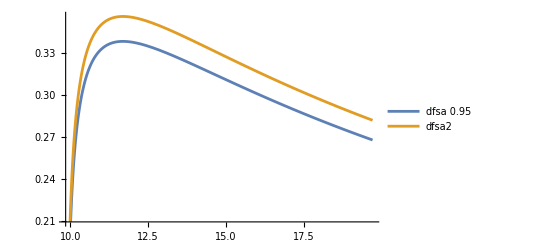

dSfa = 11.853

dSfa prime = 0.329619

dSfa prime = 0.329619

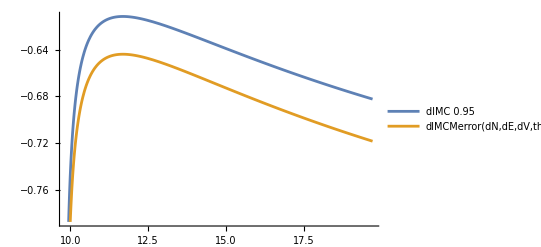

```mathematica
theta1 = Pi/10;
phi1 = Pi/4;
theta2 = Pi/6;
phi2 = 7*Pi/4;
dS = 10;
Print["Data in: {dS, θ2,ϕ2} = ",N[{dS, theta2, phi2}]];
{dN, dE, dV} = MCM[dS,theta1,phi1,theta2,phi2]
{dSout, θ2out,ϕ2out} = IMCM[dN,dE,dV,theta1,phi1];
Print["Data out: {dS, θ2,ϕ2} = ",N[{dSout, θ2out,ϕ2out}]];
dSmin = Sqrt[dN^2+dE^2+dV^2];
dSmax = 2*dSmin;
y =14.7738;
Print["Cosθ2prime = ", Cosθ2prime[y, dV]];
Print["Sinθ2prime = ", Sinθ2prime[y, dV,Cos[theta1]]];
(*dCos = D[Cosθ2[x, dV, Cos[theta1]],x] //N
Plot[{dCos*0.9,Cosθ2prime[x, dV] },{x,dSmin,dSmax}, PlotLegends->"Expressions"]
dSin = D[Sinθ2[x, dV, Cos[theta1]],x] //N
Plot[{dSin*0.9,Sinθ2prime[x, dV,Cos[theta1]] },{x,dSmin,dSmax}, PlotLegends->"Expressions"]*)
dH2 = ΔH2[dN,dE] //N;
dPsi = ΔΨ[dN,dE,Sin[phi1],Cos[phi1]] //N;
(*dSinPhi2 = D[Sinϕ2[dN,dE, Sin[theta1],Cos[theta1], Sin[phi1],Cos[phi1], Sinθ2[x, dV, Cos[theta1]],dH2,dPsi],x];
Plot[{dSinPhi2*0.9, Sinϕ2prime[dN,dE, Sin[theta1],Cos[theta1], Sin[phi1],Cos[phi1], Sinθ2[x, dV, Cos[theta1]],Sinθ2prime[x, dV,Cos[theta1]],dH2,dPsi] },{x,dSmin,dSmax}, PlotLegends->"Expressions"]

dCosPhi2 = D[Cosϕ2[dN,dE, Sin[theta1],Cos[theta1], Sin[phi1],Cos[phi1], Sinθ2[x, dV, Cos[theta1]],dH2,dPsi],x];
Plot[{dCosPhi2*0.9, Cosϕ2prime[dN,dE, Sin[theta1],Cos[theta1], Sin[phi1],Cos[phi1], Sinθ2[x, dV, Cos[theta1]],Sinθ2prime[x, dV,Cos[theta1]],dH2,dPsi] },{x,dSmin,dSmax}, PlotLegends->"Expressions"]*)

Print["Cosϕ2prime = ", Cosϕ2prime[dN,dE, Sin[theta1],Cos[theta1], Sin[phi1],Cos[phi1], Sinθ2[y, dV, Cos[theta1]],Sinθ2prime[y, dV,Cos[theta1]],dH2,dPsi]];
Print["Sinϕ2prime = ", Sinϕ2prime[dN,dE, Sin[theta1],Cos[theta1], Sin[phi1],Cos[phi1], Sinθ2[y, dV, Cos[theta1]],Sinθ2prime[y, dV,Cos[theta1]],dH2,dPsi]];

SinPhi2 = Sinϕ2[dN,dE, Sin[theta1],Cos[theta1], Sin[phi1],Cos[phi1], Sinθ2[x, dV, Cos[theta1]],dH2,dPsi];
CosPhi2 = Cosϕ2[dN,dE, Sin[theta1],Cos[theta1], Sin[phi1],Cos[phi1], Sinθ2[x, dV, Cos[theta1]],dH2,dPsi];

Cosphi2primeA = Cosϕ2prime[dN,dE, Sin[theta1],Cos[theta1], Sin[phi1],Cos[phi1], Sinθ2[x, dV, Cos[theta1]],Sinθ2prime[x, dV,Cos[theta1]],dH2,dPsi];
Sinphi2primeA = Sinϕ2prime[dN,dE, Sin[theta1],Cos[theta1], Sin[phi1],Cos[phi1], Sinθ2[x, dV, Cos[theta1]],Sinθ2prime[x, dV,Cos[theta1]],dH2,dPsi];

Print["Cosϕ2prime = ", Cosphi2primeA/.x->y];
Print["Sinϕ2prime = ", Sinphi2primeA/.x->y];


B1=  A1[Sin[theta1],Cos[phi1], Sinθ2[x, dV, Cos[theta1]],CosPhi2];
B2 = A2[Sin[theta1],Sin[phi1],Sinθ2[x, dV, Cos[theta1]],SinPhi2];
B3 = A3[Cos[theta1], Cosθ2[x, dV, Cos[theta1]]];

Print["aN = ",B1/.x->y];
Print["aE = ",B2/.x->y];
Print["aV = ",B3/.x->y];

dB1 = D[B1,x];
dB2 = D[B2,x];
dB3 = D[B3,x];
dB1a =A1prime[Sinθ2[x, dV,Cos[theta1]] ,CosPhi2,Sinθ2prime[x, dV,Cos[theta1]] ,Cosphi2primeA];
dB2a =A2prime[Sinθ2[x, dV,Cos[theta1]] ,SinPhi2,Sinθ2prime[x, dV,Cos[theta1]] ,Sinphi2primeA];
dB3a = A3prime[Cosθ2prime[x, dV]];

Print["daN = ",dB1a/.x->y];
Print["daE = ",dB2a/.x->y];
Print["daV = ",dB3a/.x->y];

Print["(ΔN^2+ΔE^2+ ΔV^2) = ",(dN^2+dE^2+ dV^2)];
Print["(A1^2+A2^2+A3^2) = ",(B1^2+B2^2+B3^2)/.x->y];
dS2dA = (dN^2+dE^2+ dV^2)/(B1^2+B2^2+B3^2)/.x->y;
Print["dS2/dA2 = ",dS2dA];
Print["Pow = ",Power[dS2dA,3/2.]];
Print["(A1 A1p+A2 A2p + A3 A3p) = ", B1 dB1a + B2 dB2a + B3 dB3a/.x->y];

(*Plot[{dB1*0.95,dB1a},{x,dSmin,dSmax}, PlotLegends->"Expressions"]
Plot[{dB2*.95,dB2a},{x,dSmin,dSmax}, PlotLegends->"Expressions"]
Plot[{dB3*0.95,dB3a},{x,dSmin,dSmax}, PlotLegends->"Expressions"]*)

dfsa = D[ΔSfα[dN,dE, dV, B1, B2, B3],x];
dfsa2=dIMCMerror[dN,dE, dV,theta1, phi1, x]+1;
Plot[{dfsa*.95,dfsa2},{x,dSmin,dSmax}, PlotLegends->"Expressions"]

Print["dSfa = ",ΔSfα[dN,dE, dV, B1, B2, B3]/.x->y]
Print["dSfa prime = ",dfsa/.x->y];
Print["dSfa prime = ",dfsa2/.x->y];

dIMC = D[IMCMerror[dN,dE, dV,theta1, phi1, x],x];
Plot[{dIMC*.95,dIMCMerror[dN,dE, dV,theta1, phi1, x]},{x,dSmin,dSmax}, PlotLegends->"Expressions"]
```

### Comparison

```mathematica
Bw=Cos[x];
Bw/.x->0
```

1

```mathematica
D[Cosθ2[ΔSfα, ΔV, Cosθ1],ΔSfα]
D[Sinθ2[ΔSfα, ΔV, Cosθ1],ΔSfα]
```

-(2 ΔV)/ΔSfα^2

(2 ΔV (-Cosθ1+(2 ΔV)/ΔSfα))/(ΔSfα^2 √(1-(-Cosθ1+(2 ΔV)/ΔSfα)^2))

```mathematica
D[Sinϕ2[ΔNx,ΔEx, Sinθ1,Cosθ1, Sinϕ1,Cosϕ1, Sinθ2x[ΔSfα],ΔH2x,ΔΨx],ΔSfα] //Simplify
```

(Sinθ1 ΔΨx ((Sinθ1 ΔEx ΔΨx)/(√(ΔH2x-(Sinθ1^2 ΔΨx^2)/Sinθ2x[ΔSfα]^2))+ΔNx Sinθ2x[ΔSfα]) Sinθ2x'[ΔSfα])/(ΔH2x Sinθ2x[ΔSfα]^3)

```mathematica
D[Cosϕ2[ΔNx,ΔEx, Sinθ1,Cosθ1, Sinϕ1,Cosϕ1, Sinθ2x[ΔSfα],ΔH2x,ΔΨx],ΔSfα] //Simplify
```

(Sinθ1 ΔΨx ((Sinθ1 ΔNx ΔΨx)/(√(ΔH2x-(Sinθ1^2 ΔΨx^2)/Sinθ2x[ΔSfα]^2))-ΔEx Sinθ2x[ΔSfα]) Sinθ2x'[ΔSfα])/(ΔH2x Sinθ2x[ΔSfα]^3)

```mathematica
D[ΔSfα[ΔN,ΔE, ΔV, A1[x], A2[x], A3[x]] ,x] //Simplify
```

-(2 ((ΔE^2+ΔN^2+ΔV^2)/(A1[x]^2+A2[x]^2+A3[x]^2))^(3/2) (A1[x] A1'[x]+A2[x] A2'[x]+A3[x] A3'[x]))/(ΔE^2+ΔN^2+ΔV^2)

```mathematica
D[A1[Sinθ1,Cosϕ1, Sinθ2[x],Cosϕ2[x]],x]
D[A2[Sinθ1,Sinϕ1,Sinθ2[x],Sinϕ2[x]],x]
D[A3[Cosθ1, Cosθ2[x]],x]
```

Sinθ2[x] Cosϕ2'[x]+Cosϕ2[x] Sinθ2'[x]

Sinϕ2[x] Sinθ2'[x]+Sinθ2[x] Sinϕ2'[x]

Cosθ2'[x]

## Test Formulas

Data in: {dS, θ2,ϕ2} = {10.,1.5708,0.523599}

Data out: {dS, θ2,ϕ2} = {10.,1.5708,0.523599}

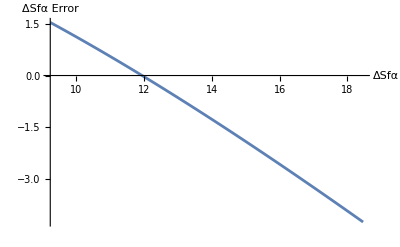

```mathematica
theta1 = Pi/16;
phi1 = Pi/6;
theta2 = Pi/2;
phi2 = Pi/6;
dS = 10;
Print["Data in: {dS, θ2,ϕ2} = ",N[{dS, theta2, phi2}]]
{dN, dE, dV} = MCM[dS,theta1,phi1,theta2,phi2];
{dSout, θ2out,ϕ2out} = IMCM[dN,dE,dV,theta1,phi1];
Print["Data out: {dS, θ2,ϕ2} = ",N[{dSout, θ2out,ϕ2out}]]
dSmin = Sqrt[dN^2+dE^2+dV^2];
dSmax = 2*dSmin;
Plot[IMCMerror[dN,dE,dV, theta1,phi1,dS],{dS,dSmin,dSmax},AxesLabel->{"ΔSfα","ΔSfα Error"}]
```

Data in: {dS, θ2,ϕ2} = {10.,0.523599,5.49779}

Data out: {dS, θ2,ϕ2} = {10.,0.523599,5.49779}

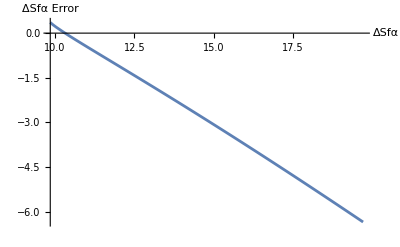

```mathematica
theta1 = Pi/10;
phi1 = Pi/4;
theta2 = Pi/6;
phi2 = 7*Pi/4;
dS = 10;
Print["Data in: {dS, θ2,ϕ2} = ",N[{dS, theta2, phi2}]]
{dN, dE, dV} = MCM[dS,theta1,phi1,theta2,phi2];
{dSout, θ2out,ϕ2out} = IMCM[dN,dE,dV,theta1,phi1];
Print["Data out: {dS, θ2,ϕ2} = ",N[{dSout, θ2out,ϕ2out}]]
dSmin = Sqrt[dN^2+dE^2+dV^2];
dSmax = 2*dSmin;
Plot[IMCMerror[dN,dE,dV, theta1,phi1,dS],{dS,dSmin,dSmax},AxesLabel->{"ΔSfα","ΔSfα Error"}]
```

## Numerical Derivative

Data in: {dS, θ2,ϕ2} = {10.,0.523599,5.49779}

Data out: {dS, θ2,ϕ2} = {10.,0.523599,5.49779}

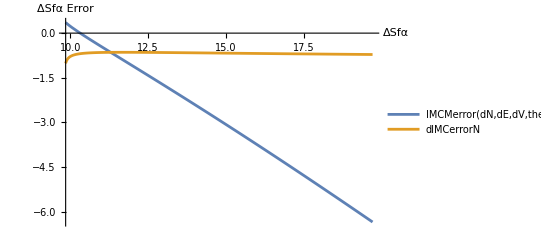

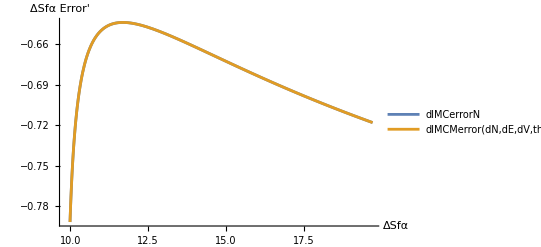

```mathematica
theta1 = Pi/10;
phi1 = Pi/4;
theta2 = Pi/6;
phi2 = 7*Pi/4;
dS = 10;
Print["Data in: {dS, θ2,ϕ2} = ",N[{dS, theta2, phi2}]]
{dN, dE, dV} = MCM[dS,theta1,phi1,theta2,phi2];
{dSout, θ2out,ϕ2out} = IMCM[dN,dE,dV,theta1,phi1];
Print["Data out: {dS, θ2,ϕ2} = ",N[{dSout, θ2out,ϕ2out}]]
dSmin = Sqrt[dN^2+dE^2+dV^2];
dSmax = 2*dSmin;
dIMCerrorN = D[IMCMerror[dN,dE,dV, theta1,phi1,x],x];
Plot[{IMCMerror[dN,dE,dV, theta1,phi1,x],dIMCerrorN},{x,dSmin,dSmax},AxesLabel->{"ΔSfα","ΔSfα Error"}, PlotLegends->"Expressions"]
Plot[{dIMCerrorN,dIMCMerror[dN,dE, dV,theta1,phi1, x]},{x,dSmin,dSmax},AxesLabel->{"ΔSfα","ΔSfα Error'"}, PlotLegends->"Expressions"]
```